# MA2330

## Chapter 3 : Determinants

You can compute the determinant by a cofactor expansion on any row or column

Theorem 1: The cofactor expansion about the i^th row 
	det(A)=∑_(j=1)^n (-1)^(i+j)a_(i,j) det(𝔸_(i,j))=∑_(j=1)^n a_(i,j) C_(i,j)=a_(i,1)C_(i,1)+…+ a_(i,n)C_(i,n)
or the j^th column
	det(A)=∑_(i=1)^n (-1)^(i+j)a_(i,j) det(𝔸_(i,j))=a_(1,j)C_(1,j)+…+ a_(n,j)C_(n,j)

It is much more efficient to compute the determinant by row reducing the matrix to Echelon form. If you row reduce a matrix A to an echelon form U without scaling any rows and r row interchanges then 
	det(A)=(-1)^r det(U)=(-1)^r Π_(i=1)^n u_(i,i)=(-1)^r u_(1,1)u_(2,2)… u_(n,n)

The square matrix equation A x=0 has non-trivial solutions iff det(A)=0.

## 5.1 Eigenvalues and Eigenvectors

The transformation A→A x for a square matrix can have special directions where the input lines up with the output. We can draw pictures for ℝ^2→ℝ^2.

```mathematica
A=({{3, 1}, {1, 3}});
Manipulate[Graphics[{
{LightBlue, EdgeForm[Blue],Disk[{0,0},4]},,
{Orange, EdgeForm[Blue],Disk[{0,0},2]},
{LightPink, EdgeForm[Red],Disk[{0,0}]},
{Red,Arrow[{{0,0},{Cos[θ],Sin[θ]}}]},
{Blue,Arrow[{{0,0},A.{Cos[θ],Sin[θ]}}]}
}],
{θ,0, 2π}]
```

It is much harder to see in 3D but you can  probably believe that there are special vector inputs that line up with the vector output for x→A x when A is a 3×3 matrix.  These vectors are called eigen-vectors!

```mathematica
A=({{3.0, 0, 1}, {0, 2, 0}, {1, 0, 3}});
Manipulate[Graphics3D[{Opacity[0.3],
{LightBlue, EdgeForm[Blue],Sphere[{0,0,0},4]},
{LightPink, EdgeForm[Red],Sphere[{0,0,0}]},
Opacity[1], Thick,
{Red,Arrow[{{0,0,0},{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}}]},
{Blue,Arrow[{{0,0,0},A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}}]}
}],
{{θ,π},0, 2π},
{{ϕ,π/2},0, π}]
```

Definition: If A v=λ v for a nontrivial vector v then the scalar λ is an eigenvalue of A and v is an eigenvector corresponding to the eigenvalue λ.

Example: Is v={1,1} an eigenvector of (3 | 1
1 | 3)? If it is what is the associated eigenvalue λ?  Yes! and λ=4.

```mathematica
({{3, 1}, {1, 3}}).{1,1}
```

{4,4}

Example: Is v={1,3,2} an eigenvector of (616 | 149 | -529
234 | 61 | -201
780 | 190 | -670)? If it is what is the associated eigenvalue λ?  Yes and λ=5.

```mathematica
({{616, 149, -529}, {234, 61, -201}, {780, 190, -670}}).{1,3,2}
```

{5,15,10}

Example: Is v={1,2,2} an eigenvector of (616 | 149 | -529
234 | 61 | -201
780 | 190 | -670)? If it is what is the associated eigenvalue λ?  No!

```mathematica
({{616, 149, -529}, {234, 61, -201}, {780, 190, -670}}).{1,2,2}
```

{-144,-46,-180}

Example: Show that λ=2 is an eigenvalue of  (3 | 1
1 | 3) and compute a corresponding eigenvector v. 
Solution: row reduce (3-2 | 1
1 | 3-2)=(1 | 1
1 | 1)~(1 | 1
0 | 0). Interpret v=(1
-1).

We know how to check if things are eigenvalues or eigenvectors. Given an eigenvalue we can compute an associated eigenvector. Given an eigenvector we can compute the matching eigenvalue.

Definition: If λ is an eigenvalue of A then the null space of (A-λ I) is the subspace of all eigenvectors associated with λ.  The eigenspace associated with an eigenvalue λ is Null(A-λ I).

Example: λ=2 is an eigenvalue of  (4 | -1 | 6
2 | 1 | 6
2 | -1 | 8) compute a basis for the corresponding eigenspace. 
Solution. Row reduce A-2 I =  (4-2 | -1 | 6
2 | 1-2 | 6
2 | -1 | 8-2)= (2 | -1 | 6
2 | -1 | 6
2 | -1 | 6)∼ (2 | -1 | 6
0 | 0 | 0
0 | 0 | 0)
Non trivial solutions are v=v_2(1/2
1
0)+v_3(-3
0
1). Eigenspace for λ=2 is span{(1/2
1
0),(-3
0
1)}.

We do not yet know how to compute eigenvalues and eigenvectors from scratch!  The problem is that the equation A v=λ v involves both v and λ!

## 5.2 Characteristic Equation

The determinant gives us a way to compute eigenvalues!

To find the eigenvalues of (2 | 3
3 | -6) we need to find when ((2 | 3
3 | -6)-λ (1 | 0
0 | 1))v=(0
0) has non-trivial solutions!  

The invertible matrix theorem gives us a bunch of equivalent conditions for this to happen: (2-λ | 3
3 | -6-λ) is not invertible; det(2-λ | 3
3 | -6-λ))=0; etc. 

We get an equation for λ from the determinant condition. 
	det(2-λ | 3
3 | -6-λ)=(2-λ)×(-6-λ)-3×3=-21+4 λ+λ^2=(λ+7)(λ-3)=0
So there are two eigenvalues λ=3 and λ=-7.

Except that the polynomials are going to get horrible we have a way to compute the eigenvalues of a matrix A if we can find the roots of the polynomial.

A scalar λ is an eigenvalue of A iff the characteristic equation det(A- λ I)=0. The characteristic polynomial of A is det(A- λ I).

### Similarity

Definition. The matrices A and B are similar if B=P A P^-1 for an invertible matrix P.

Theorem 4: If A and B are similar then they have the same characteristic polynomial.  If A and B are similar then they have the same eigenvalues.

If B=P A P^-1 then 
	A v=λ v⇒PA v=λ P v⇒P A P^-1 P v=λ P v⇒B P v=λ P v⇒B u=λ u 
where u=P v. In other words, u is an eigenvector of B associated with λ.

### Application: Discrete Dynamical System

Compute x_(n+1)=A x_n with x_0=(100
85
120
123) when A=(0.9 | 0.1 | 0.3 | 0.2
0.1 | 0.8 | 0 | 0
0 | 0.1 | 0.7 | 0
0 | 0 | 0 | 0.8).

There are four LI eigenvectors {v_1,v_2,v_3,v_4} so they span the four dimensional space!  Write 
	x_o=c_1 v_1+c_2 v_2+c_3 v_3+c_4 v_4
then 
	x_1=A x_o=c_1 A v_1+c_2 A v_2+c_3 A v_3+c_4 A v_4=c_1 λ_1 v_1+c_2 λ_2 v_2+c_3 λ_3 v_3+c_4 λ_4 v_4 
and 
	x_2=A x_1=c_1 λ_1^2 v_1+c_2 λ_2^2 v_2+c_3 λ_3^2 v_3+c_4 λ_4^2 v_4 
so ... 
	x_n=c_1 λ_1^n v_1+c_2 λ_2^n v_2+c_3 λ_3^n v_3+c_4 λ_4^n v_4 
Lets look at the eigenvalues of our A.  Lets not worry the fact that some of the eigenvalues are complex!

```mathematica
A=({{0.9, 0.1, 0.3, 0.2}, {0.1, 0.8, 0, 0}, {0, 0.1, 0.7, 0}, {0, 0, 0, 0.8}});
λs=Eigenvalues[A]
```

{1.+0. ⅈ,0.8+0. ⅈ,0.7+0.1 ⅈ,0.7-0.1 ⅈ}

So the biggest eigenvalues is λ_1=1 and the other eigenvalues (even the complex ones) are less than one in absolute value!  This means that after a while 
	x_n=c_1 λ_1^n v_1+tiny v_2+tiny v_3+tiny v_4≈c_1 v_1.
We should be able to see this

```mathematica
Clear[x]
x[0]={100,85,120,123};
x[n_]:=A.x[n-1]
MaxIter=34;
TableForm[Table[x[i],{i,1,MaxIter}],TableHeadings->{Automatic,{"N","S","E","W"}}]
x[MaxIter]/Total[x[MaxIter]]
```

| N | S | E | W
1 | 159.1 | 78. | 92.5 | 98.4
2 | 198.42 | 78.31 | 72.55 | 78.72
3 | 223.918 | 82.49 | 58.616 | 62.976
4 | 239.955 | 88.3838 | 49.2802 | 50.3808
5 | 249.658 | 94.7026 | 43.3345 | 40.3046
6 | 255.224 | 100.728 | 39.8044 | 32.2437
7 | 258.164 | 106.105 | 37.9359 | 25.795
8 | 259.498 | 110.7 | 37.1656 | 20.636
9 | 259.895 | 114.51 | 37.0859 | 16.5088
10 | 259.784 | 117.598 | 37.4112 | 13.207
11 | 259.43 | 120.056 | 37.9476 | 10.5656
12 | 258.99 | 121.988 | 38.5689 | 8.4525
13 | 258.551 | 123.49 | 39.1971 | 6.762
14 | 258.157 | 124.647 | 39.7869 | 5.4096
15 | 257.824 | 125.533 | 40.3155 | 4.32768
16 | 257.555 | 126.209 | 40.7742 | 3.46214
17 | 257.345 | 126.723 | 41.1628 | 2.76971
18 | 257.185 | 127.113 | 41.4862 | 2.21577
19 | 257.067 | 127.409 | 41.7516 | 1.77262
20 | 256.981 | 127.634 | 41.967 | 1.41809
21 | 256.92 | 127.805 | 42.1402 | 1.13447
22 | 256.878 | 127.936 | 42.2787 | 0.90758
23 | 256.849 | 128.037 | 42.3887 | 0.726064
24 | 256.829 | 128.114 | 42.4757 | 0.580851
25 | 256.817 | 128.174 | 42.5444 | 0.464681
26 | 256.809 | 128.221 | 42.5985 | 0.371745
27 | 256.804 | 128.258 | 42.6411 | 0.297396
28 | 256.801 | 128.287 | 42.6745 | 0.237917
29 | 256.8 | 128.309 | 42.7008 | 0.190333
30 | 256.799 | 128.327 | 42.7215 | 0.152267
31 | 256.799 | 128.342 | 42.7378 | 0.121813
32 | 256.799 | 128.353 | 42.7506 | 0.0974506
33 | 256.799 | 128.363 | 42.7608 | 0.0779605
34 | 256.799 | 128.37 | 42.7688 | 0.0623684

{0.599998,0.29993,0.0999271,0.000145721}

```mathematica
{v1,v2,v3,v4}=Eigenvectors[A];
v1/Total[v1]
```

{0.6+0. ⅈ,0.3+0. ⅈ,0.1+0. ⅈ,0.+0. ⅈ}

## 5.3 Diagonalization

We can pretend that most square matrices are diagonal!  The matrix A=(3 | 1
1 | 3) is similar to (4 | 0
0 | 2) since 	 A  =P (4 | 0
0 | 2)P^-1
for P=(1 | 1
1 | -1).   Where did P come from?  Well, the first column p_1=(1
1) is an eigenvector associated with λ=4 and the second column p_2=(1
-1) is an eigenvector associated with λ=2.

Definition: A is diagonalizable if A=P D P^-1 for a diagonal matrix D.

It is easy to compute powers of a diagonalizable matrix A=P D P^-1.  Clearly
	A^2=P D P^-1 P D P^-1=P D (P^-1 P) D P^-1=P D D P^-1=P D^2 P^-1
and it works similarly (the interior P^-1 P factors all collapse) for higher powers so
	A^k=P D^k P^-1.

Theorem 5: Diagonalization Theorem. An n×n matrix A is diagonalizable iff it has n Linearly Independent eigenvectors.

Why: Assume A v_i=λ_i v_i and build P= (v_1 | v_2 | … | v_n).  Then 
	A P=A (v_1 | v_2 | … | v_n)= (Av_1 | Av_2 | … | Av_n)=  (λ_1 v_1 | λ_2 v_2 | … | λ_n v_n) 
and 
	P(λ_1 | 0 | … | 0
0 | λ_2 |   | 0
⋮ |   | ⋱ | ⋮
0 | 0 | … | λ_n)=(v_1 | v_2 | … | v_n)(λ_1 | 0 | … | 0
0 | λ_2 |   | 0
⋮ |   | ⋱ | ⋮
0 | 0 | … | λ_n) =(λ_1 v_1 | λ_2 v_2 | … | λ_n v_n)
are the same so 
	A P=P D 
Since P^-1 exists we have A=P D P^-1

λ=-2 and λ=1 are evals of A=(1 | 3 | 3
-3 | -5 | -3
3 | 3 | 1).

Diagonalize A.

Write down an expression for A^n.

## 5.5 Complex Eigenvalues

Real matrices can have complex eigenvalues which always turn up as complex conjugate pairs 	
	α ± 𝕚 β.  
α is the real part and β is the imaginary part of the eval λ=α+𝕚 β  Not surprisingly the matching evecs are a also complex conjugate pair.  Functions Re (for real) and Im (for imaginary) are useful.
	Re({𝕚-1,-3𝕚+4})={-1,4}  and Im({𝕚-1,-3𝕚+4})={1,-3} .

### Diagonalization

The diagonalization theorem works provided there are enough LI eigenvectors. If A=P D P^-1 then P^-1 A P should be diagonal.

```mathematica
A=({{0.9, 0.1, 0.3, 0.2}, {0.1, 0.8, 0, 0}, {0, 0.1, 0.7, 0}, {0, 0, 0, 0.8}});
{v1,v2,v3,v4}=Eigenvectors[A];
P={v1,v2,v3,v4}ᵀ;
Chop[Inverse[P].A.P]
```

{{1.,0,0,0},{0,0.8,0,0},{0,0,0.7+0.1 ⅈ,0},{0,0,0,0.7-0.1 ⅈ}}

Complex numbers are the penalty for going all the way to diagonal in this problem

### Eigenvector Interpretation

We want to know how to think about eigenvectors. How do you explain eigenvectors to your precocious young cousin?

#### Car Example

```mathematica
A=({{0.9, 0.1, 0.3, 0.2}, {0.1, 0.8, 0, 0}, {0, 0.1, 0.7, 0}, {0, 0, 0, 0.8}});
{v1,v2,v3,v4}=Eigenvectors[A];
```

Real eigenvalues are real stretches along the real eigenvectors. In this case the first eigenvector λ=1 does not shrink or grow its eigenvector.

```mathematica
v=Chop[v1];
MaxIter=12;
TableForm[Table[v=A.v,{MaxIter}],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4
1 | -0.884652 | -0.442326 | -0.147442 | 0.
2 | -0.884652 | -0.442326 | -0.147442 | 0.
3 | -0.884652 | -0.442326 | -0.147442 | 0.
4 | -0.884652 | -0.442326 | -0.147442 | 0.
5 | -0.884652 | -0.442326 | -0.147442 | 0.
6 | -0.884652 | -0.442326 | -0.147442 | 0.
7 | -0.884652 | -0.442326 | -0.147442 | 0.
8 | -0.884652 | -0.442326 | -0.147442 | 0.
9 | -0.884652 | -0.442326 | -0.147442 | 0.
10 | -0.884652 | -0.442326 | -0.147442 | 0.
11 | -0.884652 | -0.442326 | -0.147442 | 0.
12 | -0.884652 | -0.442326 | -0.147442 | 0.

The second eigenvector gets compressed by λ=0.8 by A.

```mathematica
v=Chop[v2];
MaxIter=23;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"LogPlot"->ListLogPlot[Abs[Dataᵀ],PlotLegends->Automatic]},2]
```

123

We want to know how to interpret the complex conjugate pair 0.7±0.1 𝕚 of eigenvalues with matching eigenvectors

```mathematica
{v3,v4}
```

{{0.707107+0. ⅈ,-0.353553-0.353553 ⅈ,-0.353553+0.353553 ⅈ,0.+0. ⅈ},{0.707107+0. ⅈ,-0.353553+0.353553 ⅈ,-0.353553-0.353553 ⅈ,0.+0. ⅈ}}

We know how to check they are eigenvectors

```mathematica
{λ3,λ4}={0.7+0.1 I, 0.7 - 0.1 I};
(A-λ3 IdentityMatrix[4]).v3
(A-λ4 IdentityMatrix[4]).v4
```

{-8.32667×10^-17-8.32667×10^-17 ⅈ,2.63678×10^-16-5.55112×10^-17 ⅈ,8.32667×10^-17+2.42861×10^-16 ⅈ,0.+0. ⅈ}

{-8.32667×10^-17+8.32667×10^-17 ⅈ,2.63678×10^-16+5.55112×10^-17 ⅈ,8.32667×10^-17-2.42861×10^-16 ⅈ,0.+0. ⅈ}

Lets see if we can see what the complex eigen stuff looks like. The x_n=A x_(n-1) decays and changes signs for both the real and imaginary parts of the eigenvector!

```mathematica
v=Im[v3];
MaxIter=32;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"LogPlot"->ListLogPlot[Abs[Dataᵀ],PlotLegends->Automatic]}]
```

123

The set {v_1,v_2,Re(v_3),Im(v_3)} is LI and if 
	P=(v_1 | v_2 | Re(v_3) | Im(v_3))=(-0.884652 | 0 | 0.707107 | 0
-0.442326 | -0.408248 | -0.353553 | -0.353553
-0.147442 | -0.408248 | -0.353553 | 0.353553
0 | 0.816497 | 0 | 0)
then 
	P^-1 A P=(1. | 0 | 0 | 0
0 | 0.8 | 0 | 0
0 | 0 | 0.7 | 0.1
0 | 0 | -0.1 | 0.7).
The real and imaginary parts of the complex conjugate pair almost diagonalize the complex eigenvalues of the matrix A.  We want to look at this on small clean examples.

#### Really Clean Baby Example A=(0 | -1 1 | 0)

The characteristic equation of A=(0 | -1
1 | 0) is (-λ)^2+1=0 so it has eigenvalues λ=±ⅈ .  Row reducing 
	(A-ⅈ I)=(-ⅈ | -1
1 | -ⅈ ) 
to find an eigen vector associated with λ=ⅈ 
	(-ⅈ | -1
1 | -ⅈ )=(-ⅈ  | -1
ⅈ | -ⅈ^2)=(-ⅈ  | -1
ⅈ | 1)∼(-ⅈ  | -1
0 | 0)
so an eigen vector is (-ⅈ
1) since 
	(-ⅈ  | -1
0 | 0).(-ⅈ
1)=(-ⅈ^2-1
0)=(1-1
0)=(0
0).
You should check that (ⅈ
1) is an eigenvector for λ=-ⅈ. Let see what the iterations do.

```mathematica
A=({{0, -1}, {1, 0}});
v=RandomReal[{-1,1},2];
MaxIter=12;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"LogPlot"->ListLogPlot[Abs[Dataᵀ],PlotLegends->Automatic]},3]
```

123

#### Clean Baby Example A=(0.98 | -0.12 0.12 | 0.98)

```mathematica
A=({{0.98, -0.12}, {0.12, 0.98}});
v=RandomReal[{-1,1},2];
MaxIter=12;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"2D Plot"->ListPlot[Data,PlotLegends->Automatic,AspectRatio->Automatic]},3]
```

123

#### Another clean Baby Example A=(1.0 | -0.12 0.12 | 1.0)

```mathematica
A=({{1.0, -0.12}, {0.12, 1.0}});
v=RandomReal[{-1,1},2];
MaxIter=123;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"2D Plot"->ListPlot[Data,PlotLegends->Automatic,AspectRatio->Automatic]},3]
```

123

```mathematica
0.9+√(1-(0.9)^2)
```

1.33589

The characteristic equation of A=(0 | -1
1 | 0) is (-λ)^2+1=0 so it has eigenvalues λ=±ⅈ .  Row reducing 
	(A-ⅈ I)=(-ⅈ | -1
1 | -ⅈ ) 
to find an eigen vector associated with λ=ⅈ 
	(-ⅈ | -1
1 | -ⅈ )=(-ⅈ  | -1
ⅈ | -ⅈ^2)=(-ⅈ  | -1
ⅈ | 1)∼(-ⅈ  | -1
0 | 0)
so an eigen vector is (-ⅈ
1) since 
	(-ⅈ  | -1
0 | 0).(-ⅈ
1)=(-ⅈ^2-1
0)=(1-1
0)=(0
0).
You should check that (ⅈ
1) is an eigenvector for λ=-ⅈ. Let see what the iterations do.

```mathematica
A=({{0, -1}, {1, 0}});
v=RandomReal[{-1,1},2];
MaxIter=12;
TabView[{
"Data"->TableForm[Data=Table[v=A.v,{MaxIter}],TableHeadings->Automatic],
"Plot"->ListPlot[Dataᵀ,PlotLegends->Automatic],
"LogPlot"->ListLogPlot[Abs[Dataᵀ],PlotLegends->Automatic]}]
```

123

#### A=(a | -b b | a)=(r | 0 0 | r)(cos(ϕ) | -sin(ϕ) sin(ϕ) | cos(ϕ)) where a | = | r cos(ϕ) b | = | r sin(ϕ)

### Properties of (a | -b b | a)

The characteristic equation of A is (a-λ)^2+b^2=0.

The eigenvalues of A are λ=a± ⅈ b

A is a rotation through the angle ϕ=atan(b/a) followed by a uniform scaling of r=√(a^2+b^2).

#### A⟶(a | -b b | a)

A is a rotation through the angle ϕ=atan(b/a) followed by a uniform scaling of r=√(a^2+b^2).

#### A⟶(a | -b b | a)

If A has a complex conjugate eigenvalues a± b ⅈ then A is similar to (a | -b
b | a).

If v is the eigenvector associated with a+ b ⅈ and P=(Re(v) | Im(v)) then

A=P (a | -b
b | a)P^-1

(a | -b
b | a)=P^-1 A P

```mathematica
A=({{3.2, -12.1}, {9.2, 1.3}});
Eigenvalues[A]
{v1,v2}=Eigenvectors[A];
P1={Re[v1],Im[v1]}ᵀ;
MatrixForm[Chop[Inverse[P1].A.P1]]
```

{2.25+10.508 ⅈ,2.25-10.508 ⅈ}

(2.25 | 10.508
-10.508 | 2.25)

Any real 2×2 matrix A is similar in real arithmetic to either 
	A~(λ_1 | 0
0 | λ_2)
if A has real eigenvalues λ_1and λ_2  or 
	A~(a | -b
b | a) 
if A has complex conjugate eigenvalues a± b ⅈ. This is pretty easy to code.

```mathematica
A=RandomReal[{-1,1},{2,2}];
Eigenvalues[A]
{v1,v2}=Eigenvectors[A];
If[ Im[v1]=={0.0,0.0},
P1={v1,v2}ᵀ,
P1={Re[v1],Im[v1]}ᵀ];
MatrixForm[Chop[Inverse[P1].A.P1]]
```

{0.511622+0.394727 ⅈ,0.511622-0.394727 ⅈ}

(0.511622 | 0.394727
-0.394727 | 0.511622)

## 5.6 Discrete Dynamical Systems: x_(k+1)=A x_k

Our car problem is an example of a discrete dynamical system.  
	x_(k+1)=(0.9 | 0.1 | 0.3 | 0.2
0.1 | 0.8 | 0 | 0
0 | 0.1 | 0.7 | 0
0 | 0 | 0 | 0.8) x_k  	
The matrix A says where the cars rented from the North South East and West locations are returned to each day.

Biological problems produce similar systems.  An age-stage biological model splits a population by age:

The first entry of x is the population less than one.

The second entry of x is the population between one and two.

The p^th entry of x is the number between p and p+1.

Suppose the biological population is people. How does this vector change from year to year?  If the age stages are by year how long do our vectors need to be?

Discrete control theory problems add a control vector u_k to get the dynamical system 
	x_(k+1)=A x_k+u_k
The goal is to choose u_k to steer the system to some desired state.  The wiki page is probably too much
	https://en.wikipedia.org/wiki/Control_theory
 Any engineering school has a bunch of control theory courses which use a LOT of Linear Algebra
	 https://www.mtu.edu/gradschool/programs/certificates/control-systems/

We know how to write down the solution of
	x_(k+1)=A x_k  with initial condition x_0∈ℝ^n given
Assume A is diagonalizable, then we have eigenvectors v_1,v_2,…,v_n which span ℝ^n so 
	x_0=c_1 v_1+c_2 v_2+…+c_n v_n
so since A v_i=λ_i v_i we have 
	x_1 | = | A x_0 | = | c_1 A v_1+c_2 A v_2+…+c_n A v_n      
  |   |   |   | c_1 λ_1 v_1+c_2 λ_2 v_2+…+c_n λ_n v_n
as a result
	x_k | = | (c_1(λ_1))^k v_1+(c_2(λ_2))^k v_2+…+(c_n(λ_n))^k v_n
Eigenvalues are usually sorted big to little i.e. |λ_i|≥|λ_(i+1)|.  Assume this is the case and that the first inequality is actually|λ_1| >|λ_2| then 
	  x_k | = | (c_1(λ_1))^k v_1+(c_2(λ_2))^k v_2+…+(c_n(λ_n))^k v_n
x_k | = |  (λ_1)^k(c_1 v_1+(c_2(λ_2/λ_1))^k v_2+…+(c_n(λ_n/λ_1))^k v_n)
x_k | ≈ | (λ_1)^k c_1 v_1                                                                         
In words, the eigenvector associated with an isolated dominant eigenvalue determines the long time behavior.  If the dominant eigenvalue is greater than one in magnitude the solution grows exponentially. If the dominant eigenvalue is less than one in magnitude the solution decays exponentially.

### Pictures of Dynamical Systems

It is pretty easy to plot solutions of Dynamical Systems in 2 or 3 dimensions.

```mathematica
Options[Arrow]
```

{}

```mathematica
?Arrow
```

```mathematica
VectorPlot
```

VectorPlot

```mathematica
DySysPlot2D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/11},
Data=Table[ 
x[0]={Cos[θ],Sin[θ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{θ,Δθ,2π,Δθ}];
ListPlot[Data,AspectRatio->Automatic,
Prolog->{Green, Circle[{0,0},1]},
Epilog->{Black,Arrowheads[Small],Thin,Map[Arrow,Data]},
PlotLabel->A]
]
```

```mathematica
DySysPlot2D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/11},
Data=Table[ 
x[0]={Cos[θ],Sin[θ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{θ,Δθ,2π,Δθ}];
ListPlot[Data,AspectRatio->Automatic,
Prolog->{Green, Circle[{0,0},1]},
Epilog->{Black,Arrowheads[Small],Thin,Map[Arrow,Data]},
PlotLabel->A]
]
```

```mathematica
DySysPlot3D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/6},
Data=Flatten[Table[ 
x[0]={Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{ϕ,Δθ,π-Δθ,Δθ},{θ,Δθ,2π,Δθ}],1];
Show[
Graphics3D[{Opacity[0.2],LightGreen,Sphere[{0,0,0},1]}],
ListLinePlot3D[Data,BoxRatios->Automatic,
PlotMarkers->{"Point",Small},
PlotStyle->Thin,
PlotLabel->A]
]]
```

```mathematica
A=({{0.5, 0.4, 0}, {-0.104, 1.1, 0}, {0.1, 0, 0.9}});
DySysPlot3D[A]
```

-Graphics3D-

```mathematica
A=({{0.5, 0.4}, {-0.104, 1.1}});
DySysPlot2D[A]
```

-Graphics-

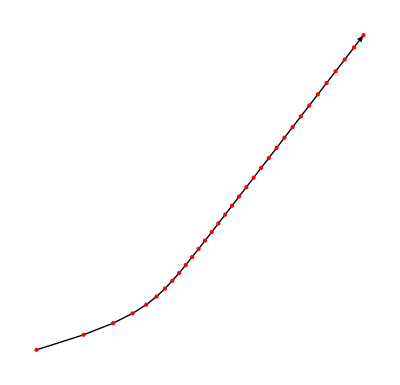

```mathematica
A=({{0.5, 0.4}, {-0.104, 1.1}});
x[k_]:=A.x[k-1]
x[0]={0.1,0.2};
maxStep=32;
Data=Table[x[k],{k,0, maxStep}];
Graphics[{Arrow[Data], Red,Point[Data]}]
```

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``)row_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
ANew=Simplify[ANew];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```